# Moments of The lattice An

## Ramanan’s Recursion

```mathematica
Clear[F]
F[0,k_,m_,a_,b_]:=0;
F[n_,0,0,a_,b_]:=(a-b)^n;
F[1,k_,m_,a_,b_]:=(a^(2*k+m+1) -b^(2*k+m+1))/(2*k+m+1);
F[n_,k_,m_,a_,b_]:=
F[n,k,m,a,b]=Expand[Sum[Sum[Binomial[k,j]*Binomial[m,jd]*(a^(2*j+jd+1)-b^(2*j+jd+1))/(2*j+jd+1)*F[n-1,k-j,m-jd,a,b],{jd,0,m}],{j,0,k}]];
```

## The G recursion

```mathematica
Clear[G];
G[n_,0,0,a_,b_]:=1;
G[1,k_,m_,a_,b_]:=
Sum[a^(2*k+m-i)*b^i,{i,0,2*k+m}]/(2*k +m+1);
G[n_,k_,m_,a_,b_]:=G[n,k,m,a,b]=Expand[Sum[Sum[Binomial[k,j]*Binomial[m,jd]*Sum[a^(2*j+jd-i)*b^i,{i,0,2*j+jd}]/(2*j +jd+1)*G[n-1,k-j,m-jd,a,b],{jd,0,m}],{j,0,k}]];
```

## The B function

```mathematica
B[n_,t_,a_,b_] := Sum[Sum[(-1/(n+1))^(t-j1)*2^j2*(a+b)^j2*Factorial[t]/Factorial[j1]/Factorial[j2]/Factorial[t-j1-j2]*G[n-1,j1,j2+2*(t-j1-j2),a,b],{j2,0,t-j1}],{j1,0,t}];
```

## The integral polynomial

```mathematica
Littlec[n_,a_,b_] = a^2 + b^2 - (a+b)^2/(n+1);
BP[n_,m_,a_,b_]:=Sum[Binomial[m,k]*Littlec[n,a,b]^k*B[n,m-k,a,b],{k,0,m}];
BPyz[n_,m_,y_,z_] := BP[n,m,y - 1/2 ,y-z-1/2];
FullSimplify[BPyz[6,2,y,z]]
```

(671 z^4)/882

## The polynomial conversion

```mathematica
funT[n_,k_] := Sum[1/x,{x,n, n+k}]/(k+1);
eucpower[n_,m_] := n*Fold[Function[{s,v}, s + Fold[Function[{ss,vv}, ss + vv],0,v]],0,MapIndexed[Function[{v,d}, v*funT[n+d[[2]]-1, d[[1]]-1]], CoefficientList[BPyz[n,m,y,z],{y,z}],{2}]]
```

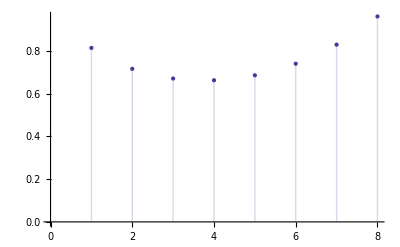

```mathematica
DiscretePlot[eucpower[8,n],{n, 1,8}]
```

```mathematica
T =Table[eucpower[8,n],{n, 8}]
```

{22/27,871/1215,10279/15309,652817/984150,6690014/9743085,4223148232/5699704725,2838633274/3419822835,100679860228/104646578751}

```mathematica
T25 = T
```

{22/27,871/1215,10279/15309,652817/984150,6690014/9743085,4223148232/5699704725,2838633274/3419822835,100679860228/104646578751}